## 3. DOMAČA NALOGA

Spodnji graf prikazuje omrežje, v katerem ima vsaka povezava tako minimalen
kot maksimalen dopusten pretok. Ugotovite, kolikšen je maksimalen pretok od S do T.

Najprej narišemo graf.

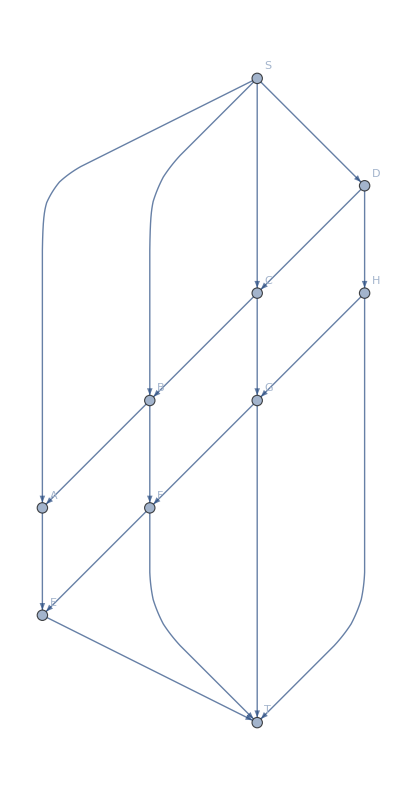

```mathematica
Graph[{s,a,b,c,d,e,f,g,h,t}, {s-> a, s->b, s->c, s->d, a->e, b->f, c->g, d->h, e->t, f->t, g->t, h->t, d->c, c->b, b->a, h->g, g->f, f->e}, VertexLabels-> {s-> "S", a->"A", b->"B", c->"C", d->"D", e->"E", f->"F",g ->"G", h->"H", t->"T"}]
```

Nalogo rešujemo kot linearni program. Iščemo max u_1+ u_2+u_3+ u_4. (to je SA, SB, SC, SD) pri pogojih uteži in Kirchoffovih pogojih.

indeksi povezav:
1 = SA (2-4) , 2 = SB ( 2-4), 3 = SC(10-18) ,  4 = SD (8-18),  5 = DC (0-6), 
6 = CB (2-6), 7 = BA (4-6), 8 = AE (6-8), 9 = BF (4-10), 10 =  CG (4-6), 
11 = DH (6-8), 12 = HT (4-10), 13 = GT (4-6), 14 = FT (4-6), 15 = ET (11-16), 
16 = HG(2-6), 17  = GF (6-6), F18 = FE(4-5)

Kirchoffovi pogoji:
SA +BA = AE, SB+CB = BA+BF, SC + DC = CB+CG, SD = DC + DH, 
AE+FE=ET,  BF + GF = FE+FT, CG+ HG = GF +GT, DH =HG + HT

oziroma z indeksi:
1+7 = 8, 2+6 = 7+9, 3+5 = 10 +6, 4 = 5+11, 
8 +18 = 15, 9+17 = 18 + 14, 10 + 16 = 13 + 17, 11 = 16+12

```mathematica
Maximize[{Subscript[u, 1]+ Subscript[u, 2] + Subscript[u, 3] + Subscript[u, 4] ,2≤  Subscript[u, 1]≤4, 2≤  Subscript[u, 2] ≤4, 10≤  Subscript[u, 3] ≤18, 8≤  Subscript[u, 4] ≤18, 0≤ Subscript[u, 5]≤6 ,2≤ Subscript[u, 6] ≤6, 4≤  Subscript[u, 7]≤ 6,6≤  Subscript[u, 8]≤8, 4≤  Subscript[u, 9] ≤10, 4≤  Subscript[u, 10] ≤6, 6≤  Subscript[u, 11] ≤8, 4≤ Subscript[u, 12]≤10 ,4≤ Subscript[u, 13] ≤6, 4≤  Subscript[u, 14]≤ 6 , 11≤  Subscript[u, 15]≤ 16 , 2≤  Subscript[u, 16]≤ 6, 6≤  Subscript[u, 17]≤ 6, 4≤  Subscript[u, 18]≤ 5,Subscript[u, 1]+Subscript[u, 7]== Subscript[u, 8] ,Subscript[u, 2]+Subscript[u, 6]== Subscript[u, 9] + Subscript[u, 7],Subscript[u, 3]+Subscript[u, 4]== Subscript[u, 10] + Subscript[u, 6] , Subscript[u, 4]==  Subscript[u, 5]+Subscript[u, 11], 
Subscript[u, 8]+Subscript[u, 18]== Subscript[u, 15] , Subscript[u, 9]+Subscript[u, 17]== Subscript[u, 18] + Subscript[u, 14], Subscript[u, 10]+Subscript[u, 16]== Subscript[u, 13] + Subscript[u, 17], Subscript[u, 11]== Subscript[u, 16] + Subscript[u, 12], Subscript[u, 11]+Subscript[u, 7]== Subscript[u, 8]}, {Subscript[u, 1], Subscript[u, 2] , Subscript[u, 3] , Subscript[u, 4] ,Subscript[u, 5],Subscript[u, 6], Subscript[u, 7],Subscript[u, 8], Subscript[u, 9], Subscript[u, 10], Subscript[u, 11] , Subscript[u, 12] , Subscript[u, 13]  Subscript[u, 14], Subscript[u, 15] , Subscript[u, 16] , Subscript[u, 17] ,Subscript[u, 18] }]
```

Maximize::ivar: u_5+u_12+u_16 is not a valid variable.

Maximize[{u_1+u_2+u_3+u_5+u_12+u_16,2≤u_1≤4,2≤u_2≤4,10≤u_3≤18,8≤u_5+u_12+u_16≤18,0≤u_5≤6,2≤u_6≤6,4≤u_7≤6,6≤u_8≤8,4≤u_9≤10,4≤u_10≤6,6≤u_12+u_16≤8,4≤u_12≤10,4≤u_13≤6,4≤u_14≤6,11≤u_15≤16,2≤u_16≤6,6≤u_17≤6,4≤u_18≤5,u_1+u_7==u_8,u_2+u_6==u_7+u_9,u_3+u_5+u_12+u_16==u_6+u_10,True,u_8+u_18==u_15,u_9+u_17==u_14+u_18,u_10+u_16==u_13+u_17,True,u_7+u_12+u_16==u_8},{u_1,u_2,u_3,u_5+u_12+u_16,u_5,u_6,u_7,u_8,u_9,u_10,u_12+u_16,u_12,u_13 u_14,u_15,u_16,u_17,u_18}]

```mathematica
Maximize[{Subscript[u, 1]+ Subscript[u, 2] + Subscript[u, 3] + Subscript[u, 4] ,2≤  Subscript[u, 1]≤4, 2≤  Subscript[u, 2] ≤4, 10≤  Subscript[u, 3] ≤18, 8≤  Subscript[u, 4] ≤18, 0≤ Subscript[u, 5]≤6 ,2≤ Subscript[u, 6] ≤6, 4≤  Subscript[u, 7]≤ 6,6≤  Subscript[u, 8]≤8, 4≤  Subscript[u, 9] ≤10, 4≤  Subscript[u, 10] ≤6, 6≤  Subscript[u, 11] ≤8, 4≤ Subscript[u, 12]≤10 ,4≤ Subscript[u, 13] ≤6, 4≤  Subscript[u, 14]≤ 6 , 11≤  Subscript[u, 15]≤ 16 , 2≤  Subscript[u, 16]≤ 6, 6≤  Subscript[u, 17]≤ 6, 4≤  Subscript[u, 18]≤ 5,Subscript[u, 1]+Subscript[u, 7]≤  Subscript[u, 8] , Subscript[u, 1]+Subscript[u, 7]≥   Subscript[u, 8], Subscript[u, 2]+Subscript[u, 6]≤  Subscript[u, 9] + Subscript[u, 7], Subscript[u, 2]+Subscript[u, 6]≥   Subscript[u, 9] + Subscript[u, 7],Subscript[u, 3]+Subscript[u, 4] ≤  Subscript[u, 10] + Subscript[u, 6] , Subscript[u, 3]+Subscript[u, 4] ≥   Subscript[u, 10] + Subscript[u, 6] ,Subscript[u, 4]≤  Subscript[u, 5]+Subscript[u, 11], Subscript[u, 4]≥    Subscript[u, 5]+Subscript[u, 11], Subscript[u, 8]+Subscript[u, 18]≤  Subscript[u, 15] ,  Subscript[u, 8]+Subscript[u, 18]≥   Subscript[u, 15], Subscript[u, 9]+Subscript[u, 17]≤  Subscript[u, 18] + Subscript[u, 14],  Subscript[u, 9]+Subscript[u, 17]≥   Subscript[u, 18] + Subscript[u, 14], Subscript[u, 10]+Subscript[u, 16]≤  Subscript[u, 13] + Subscript[u, 17], Subscript[u, 10]+Subscript[u, 16]≥   Subscript[u, 13] + Subscript[u, 17], Subscript[u, 11]≤  Subscript[u, 16] + Subscript[u, 12], Subscript[u, 11]≥   Subscript[u, 16] + Subscript[u, 12], Subscript[u, 11]+Subscript[u, 7]≤  Subscript[u, 8], Subscript[u, 11]+Subscript[u, 7]≥   Subscript[u, 8]}, {Subscript[u, 1], Subscript[u, 2] , Subscript[u, 3] , Subscript[u, 4] ,Subscript[u, 5],Subscript[u, 6], Subscript[u, 7],Subscript[u, 8], Subscript[u, 9], Subscript[u, 10], Subscript[u, 11] , Subscript[u, 12] , Subscript[u, 13]  Subscript[u, 14], Subscript[u, 15] , Subscript[u, 16] , Subscript[u, 17] ,Subscript[u, 18] }]
```

GAJA RIHAR 26.3.2018